{{226,5},{194,6},{170,7},{156,8},{141,9},{136,10},{125,11},{117,12},{107,13},{95,15},{75,20},{55,30},{44,40},{37,50},{33,60},{30,70},{27,80},{26,90},{22,120},{20,150}}

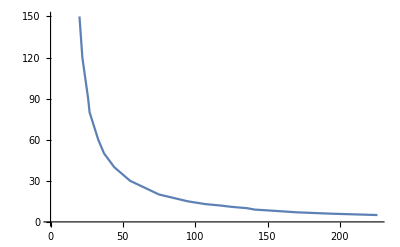

84134.5-0.0390032 x-53553.8 ArcTan[x^2]

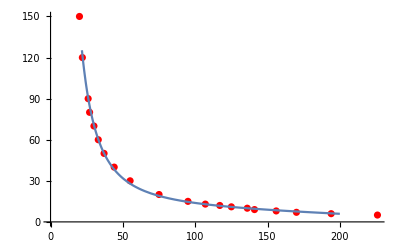

```mathematica
data = {
{226,5},
{194,6},
{170,7},
{156,8},
{141,9},
{136,10},
{125,11},
{117,12},
{107,13},
{95,15},
{75,20},
{55,30},
{44,40},
{37,50},
{33,60},
{30,70},
{27,80},
{26,90},
{22,120},
{20,150}
}
ListPlot[data, Joined->True]
func =Fit[data, {1,x,ArcTan[x^2]},x]
Show[ListPlot[data, PlotStyle->Red], Plot[{func}, {x, 0, 200}]]
```